# Chapter. Other numerical methods

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->63,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12],Cell[TextData[{"Other numerical methods"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","The Thomas algorithm","Extending the Thomas algorithm","Runge-Kutta methods","Iterative methods","Numerical solutions to Volterra equations of the first kind","Numerical solutions to Volterra equations of the second kind","Summary","Further Reading"},#]&)]],FontFamily->"Arial",FontSize->12],Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
```

```mathematica
ClearNotations[];
Symbolize[Subscript[c, _]];
Symbolize[Subscript[c, _]^_];
```

```mathematica
SetOptions[Plot,
Axes->False,
BaseStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Frame->True,
GridLines->None,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->AbsoluteThickness[1]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Frame->True,
GridLines->None,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->AbsoluteThickness[1],
Joined->True];
```

```mathematica
SetOptions[ListLogPlot,
(*BaseStyle->Directive[FontFamily->"Arial",11,Bold,GrayLevel[0.2]],*)
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->AbsolutePointSize[5],
PlotRange->All,
Joined->False];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
optionC={
PlotRange-> {{-10,10}, {0, -0.5}},
FrameTicks:>{ticks1[-10,10,5,5],ticks1[.6,-.6,-.2,5],ticks2[-10,10,5,5],ticks2[.6,-.6,-.2,5]},
RotateLabel->False,
FrameLabel->{Style["nF/RT(E-E°)",FontFamily->"Times New Roman",Italic,10],Style["χ",FontFamily->"Times New Roman",Italic,10],None,None}};
```

```mathematica
ClearAll[LowerDiagonalMatrix,UpperDiagonalMatrix];

LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≥#2,f[##],0]&,{n,n}];

UpperDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≤#2,f[##],0]&,{n,n}];
```

```mathematica
ClearAll[makeDiagonals,makeMatrix,implicitSolve];

makeDiagonals[m_Integer,α_]:=
	Module[{x,y,z},
		x=Table[-α,{m-3}];
		z=Table[-α,{m-3}];
		y=Table[1.+2.*α,{m-2}];
{x,y,z}
];

makeMatrix[m_Integer,α_]:=Module[{x,y,z},
{x,y,z}=makeDiagonals[m,α];
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,m-2},{j,m-2}]
];

implicitSolve[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]+=d;
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

NestList[solveNext,initial,n-1]
]
```

```mathematica
optionD={
 Frame->{True,True,False,False},
FrameLabel-> {"n","t",None,None},
(*PlotMarkers->(Style[#,16]&/@{★,•,◼,◆}),*)
RotateLabel-> False};
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

Chapter 2 examined the use of explicit and implicit methods to solve equations for the relatively simple case of a potential step to the limiting current region. In Chapter 3 we examined methods to enhance the accuracy and speed of computations. In those chapters the problem reduced to the solution of matrix equation comprising a tridiagonal matrix. The solution, which is known as the Thomas algorithm, was obtained using a pre-programmed function to solve the tridiagonal matrix. In this chapter we examine the underlying steps involved in the Thomas algorithm and extend the solution method to more complex problems. Finally, when attempting a Laplace transform solution to an electrochemical problem we frequently find that the solution yields equations known as Volterra equations that must be solved numerically. We examine a common method to solve Volterra equations in this chapter.

## Chapter.Section The Thomas algorithm

Tridiagonal matrix solver that come with very early versions of Mathematica used the Thomas algorithm though the result was rather slow depending on which version of Mathematica you were using. The Thomas algorithm uses an LU decomposition and backsubstitution to solve the matrix equation. LU decomposition becomes very efficient when the matrix is tridiagonal. LU decomposition decomposes a matrix into two matrices comprising upper and lower elements:

```mathematica
ClearAll[m,upper,lower,mat,U,L];

mat = Array[m, {3,3}]//MatrixForm;
upper=UpperDiagonalMatrix[U, 3] //MatrixForm;
lower=LowerDiagonalMatrix[L,3] //MatrixForm;
mat==upper.lower
```

(m[1,1] | m[1,2] | m[1,3]
m[2,1] | m[2,2] | m[2,3]
m[3,1] | m[3,2] | m[3,3])==(U[1,1] | U[1,2] | U[1,3]
0 | U[2,2] | U[2,3]
0 | 0 | U[3,3]).(L[1,1] | 0 | 0
L[2,1] | L[2,2] | 0
L[3,1] | L[3,2] | L[3,3])

For a tridiagonal matrix this procedure simplifies considerably. Starting with the equation A·u=b the matrix A can be decomposed into two other matrices L and U, such that A=L·U, for example:

(y_1 | z_1 |   |   |  
x_2 | y_2 | z_2 |   |  
  | ⋱ | ⋱ | ⋱ |  
  |   | x_(m-1) | y_(m-1) | z_(m-1)
  |   |   | x_m | y_m)=(α_1 |   |   |   |  
x_2 | α_2 |   |   |  
  | ⋱ | ⋱ |   |  
  |   | x_(m-1) | α_(m-1) |  
  |   |   | x_m | α_m)·(1 | β_1 |   |   |  
  | 1 | β_2 |   |  
  |   | ⋱ | ⋱ |  
  |   |   | 1 | β_(m-1)
  |   |   |   | 1)

The elements in A can then be written in terms of the elements in L and U. To see this we first generate these matrices:

```mathematica
ClearAll[x,y,z,α,β];

mat=Table[Switch[i-j,-1,Subscript[z,i],0,Subscript[y,i],1,Subscript[x,i],_,0],{i,5},{j,5}];
mat//MatrixForm
```

(y_1 | z_1 | 0 | 0 | 0
x_2 | y_2 | z_2 | 0 | 0
0 | x_3 | y_3 | z_3 | 0
0 | 0 | x_4 | y_4 | z_4
0 | 0 | 0 | x_5 | y_5)

```mathematica
lower=Table[Switch[i-j,0,Subscript[α,i],1,Subscript[x,i],_,0],{i,5},{j,5}];
lower//MatrixForm
```

(α_1 | 0 | 0 | 0 | 0
x_2 | α_2 | 0 | 0 | 0
0 | x_3 | α_3 | 0 | 0
0 | 0 | x_4 | α_4 | 0
0 | 0 | 0 | x_5 | α_5)

```mathematica
upper=Table[Switch[i-j,-1,Subscript[β,i],0,1,_,0],{i,5},{j,5}];
upper//MatrixForm
```

(1 | β_1 | 0 | 0 | 0
0 | 1 | β_2 | 0 | 0
0 | 0 | 1 | β_3 | 0
0 | 0 | 0 | 1 | β_4
0 | 0 | 0 | 0 | 1)

The dot product of L and U is

```mathematica
lower.upper//MatrixForm
```

(α_1 | α_1 β_1 | 0 | 0 | 0
x_2 | α_2+x_2 β_1 | α_2 β_2 | 0 | 0
0 | x_3 | α_3+x_3 β_2 | α_3 β_3 | 0
0 | 0 | x_4 | α_4+x_4 β_3 | α_4 β_4
0 | 0 | 0 | x_5 | α_5+x_5 β_4)

Comparing the original matrix with the matrix L·U allows α_i and β_i to be expressed in terms of the known values of x_i, y_i, and z_i. Solving for y_i gives

y_i =α_i+x_i β_(i-1)	for i>1

with y_1=α_1 therefore

α_i=y_i-x_i β_(i-1)	for i>1

Solving for z gives

z_i=α_i β_i

therefore

β_i=z_i/α_i

The values of α_i and β_i can be calculated for 1≤i≤m.

alpha[previous_Real,j_Integer]:=(y⟦j⟧-x⟦j⟧*z⟦j-1⟧/previous);
α=FoldList[alpha,y⟦1⟧,Range[2,Length[b]]];

The back substitution proceeds via an intermediate vector f where b=L·f, therefore f=L^-1·b.

(b_1
b_2
⋮
b_(m-1)
b_m)=(α_1 |   |   |   |  
x_2 | α_2 |   |   |  
  | ⋱ | ⋱ |   |  
  |   | x_(m-1) | α_(m-1) |  
  |   |   | x_m | α_m)·(f_1
f_2
⋮
f_(m-1)
f_m)

```mathematica
ClearAll[b,f,u];

bVec=Table[Subscript[b,i],{i,1,5}];
fVec=Table[Subscript[f,i],{i,1,5}];
lower.fVec//MatrixForm
```

(f_1 α_1
f_1 x_2+f_2 α_2
f_2 x_3+f_3 α_3
f_3 x_4+f_4 α_4
f_4 x_5+f_5 α_5)

It is straightforward to relate b to f.

b_i=x_i f_(i-1)+α_i f_i	for i>1

with b_1=α_1 f_1 and therefore

f_i=(b_i-x_i f_(i-1))/α_i	for i>1

with f_1=b_1/α_1, allowing the values of f to be calculated from one to m. Note that the subscripts in these equations refer to row number whereas the code references the parts of the three vectors, x, y, and z.

eff[previous_Real,j_Integer]:=((b⟦j⟧-x⟦j-1⟧*previous)/α⟦j⟧);

f=FoldList[eff,b⟦1⟧/α⟦1⟧,Range[2,Length[b]]];

The final step is a forward substitution. Since b=A·u=L·U·u and b=L·f we know that f=U·u therefore u=U^-1·f.

(f_1
f_2
⋮
f_(m-1)
f_m)=(1 | β_1 |   |   |  
  | 1 | β_2 |   |  
  |   | ⋱ | ⋱ |  
  |   |   | 1 | β_(m-1)
  |   |   |   | 1)·(u_1
u_2
⋮
u_(m-1)
u_m)

```mathematica
uVec=Table[Subscript[u,i],{i,1,5}];
upper.uVec//MatrixForm
```

(u_1+u_2 β_1
u_2+u_3 β_2
u_3+u_4 β_3
u_4+u_5 β_4
u_5)

Beginning with the final term u_m=f_m and for other terms

f_i=u_i+β_i u_(i+1)

therefore

u_i =f_i-β_i u_(i+1).

u[previous_Real,j_Integer]:=f⟦j⟧-z⟦j⟧*previous/α⟦j⟧;

FoldList[u,Last[f],Range[Length[b]-1,1,-1]]//Reverse

Combining the lines of code above gives:

```mathematica
ClearAll[thomas];

thomas[x_List,y_List,z_List,b_List]:= Module[{len=Length[b],a,α,eff,f,u},
   
a[previous_Real,j_Integer]:=(y⟦j⟧-x⟦j-1⟧*z⟦j-1⟧/previous);
    
u[previous_Real,j_Integer]:=(f⟦j⟧-z⟦j⟧*previous/α⟦j⟧);

eff[previous_Real,j_Integer]:=N[((b⟦j⟧-x⟦j-1⟧*previous)/α⟦j⟧)]; 

α=FoldList[a,N[y⟦1⟧],Range[2,len]];
   
 f=FoldList[eff,N[b⟦1⟧/y⟦1⟧],Range[2,len]];
   
 FoldList[u,Last[f],Range[len-1,1,-1]]//Reverse];
```

This function can be tested by generating some diagonals and the vector b and compared to the solution using LinearSolve.

```mathematica
ClearAll[makeDiagonals,makeMatrix];

makeDiagonals[m_Integer,α_]:=Module[{x,y,z},
		x=Table[-α,{m-3}];
		z=Table[-α,{m-3}];
		y=Table[1.+2.*α,{m-2}];
{x,y,z}
];

makeMatrix[m_Integer,α_]:=Module[{x,y,z},
{x,y,z}=makeDiagonals[m,α];
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,m-2},{j,m-2}]
];
```

An implicit solver function can be made with a slight modification to the solvers used in Chapter 2.

```mathematica
ClearAll[implicitSolve2];

implicitSolve2[m_Integer,n_Integer,α_]:=Module[{solveNext,mat,initial,x,y,z},

{x,y,z}=makeDiagonals[m,α];
initial=ConstantArray[1.,{m}];
solveNext[x_,y_,z_][α1_]:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+α1;
Flatten[{0.,thomas[x,y,z,b],1.}]
]&;

Transpose@NestList[solveNext[x,y,z][α],initial,n-1]
]
```

The efficiency of the tridiagonal solver can be tested by comparing to the fastest solvers from Chapter 2.

```mathematica
ClearAll[𝔻,n,res1,res2];

𝔻=1.5;(*model diffusion coefficient*)
n={100,200,400,600,800,1000};

(*LinearSolve method*)
res1= Map[Timing[(m=1+Ceiling[6*√(𝔻*(#-1))];implicitSolve[m, #,𝔻];)]&,n]
(*Thomas algorithm*)
res2= Map[Timing[(m=1+Ceiling[6*√(𝔻*(#-1))];implicitSolve2[m, #,𝔻];)]&,n]
```

{{0.009458,Null},{0.023689,Null},{0.05903,Null},{0.090835,Null},{0.14957,Null},{0.203021,Null}}

{{0.105224,Null},{0.860733,Null},{1.40096,Null},{2.04456,Null},{2.87292,Null},{3.76233,Null}}

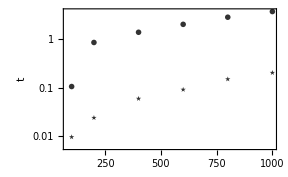
-Graphics-★implicitSolve1•implicitSolve2

```mathematica
Clear[res1a,res2a];

res1a=Transpose[{n,res1⟦All,1⟧}];
res2a=Transpose[{n,res2⟦All,1⟧}];

Labeled[
ListLogPlot[{res1a,res2a},PlotMarkers->{★,•},optionD],
Row[Flatten@Riffle[MapIndexed[{Style[ToString@#1,Black,16],Spacer[4],Style["implicitSolve"<>ToString[0+First[#2]],FontFamily->"Courier",10,Bold]}&,{★,•}],Spacer[12]]],{{Bottom,Center}}]
```

Our version can be compiled in order to reduce the computation time.

```mathematica
ClearAll[tridiagonalSolve];

tridiagonalSolve = Compile[{{x, _Real, 1}, {y, _Real, 1}, {z, _Real, 1}, {b, _Real, 1}},

Module[{len=Length[b],solution=Table[0.,{Length[b]}],aux = 0.,β=Table[0.,{Length[b]}],iter = 0},

aux=1/y[[1]];
solution⟦1⟧=b⟦1⟧ aux;
Do[β⟦iter⟧=z⟦iter-1⟧ aux;
aux=1/(y⟦iter⟧-x⟦iter-1⟧ β⟦iter⟧);
solution⟦iter⟧=(b⟦iter⟧-x⟦iter-1⟧ solution⟦iter-1⟧) aux,
{iter,2,len}];
Do[solution⟦iter⟧-=β⟦iter+1⟧ solution⟦iter+1⟧,
{iter,len-1,1,-1}];
solution]
];
```

```mathematica
ClearAll[thomasSolver];

thomasSolver[m_Integer,n_Integer,α_]:=Module[{solveNext,mat,initial,x,y,z},
{x,y,z}=makeDiagonals[m,α];
initial=ConstantArray[1.,{m}];
solveNext[x_,y_,z_][α1_]:=Module[{tmp,b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+α1;
Flatten[{0.,tridiagonalSolve[x,y,z,b],1.}]
]&;

Transpose@NestList[solveNext[x,y,z][α],initial,n-1]
]
```

```mathematica
Clear[res3,res3a];
res3= Map[Timing[(m=1+Ceiling[6*√(𝔻*(#-1))];thomasSolver[m, #,𝔻];)]&,n]
res3a=Transpose[{n,res3⟦All,1⟧}];
```

{{0.006945,Null},{0.067431,Null},{0.164876,Null},{0.290039,Null},{0.437953,Null},{0.609163,Null}}

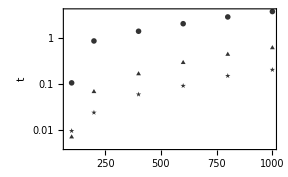
-Graphics-★implicitSolve1•implicitSolve2▲thomasSolver

```mathematica
Labeled[
ListLogPlot[{res1a,res2a,res3a},
PlotMarkers->{★,•,▲},optionD
],
Row[Flatten@Riffle[(MapIndexed[{Style[ToString@#1,Black,16],Spacer[4],Style["implicitSolve"<>ToString[0+First[#2]],FontFamily->"Courier",10,Bold]}&,{★,•,▲}] /. "implicitSolve3"->"thomasSolver"),Spacer[12]]],{{Bottom,Center}},
LabelStyle->Directive[FontFamily->"Courier",10,Bold]]
```

## Chapter.Section Extending the Thomas algorithm

The Thomas algorithm can be extended to solve matrix equation where the matrix elements are themselves square matrices and the vector elements are themselves vectors. This extended version of the Thomas algorithm has been used by Rudolph in the general electrochemical simulator which is the basis of the DigiSim™ simulator. Extending the method outlined in the previous section to cover these types of problems is relatively straightforward. Starting again with the matrix equation M·u=b the matrix M can be decomposed into two other matrices L and U, M=L·U, for example:

(Y_1 | Z_1 |   |   |  
X_2 | Y_2 | Z_2 |   |  
  | ⋱ | ⋱ | ⋱ |  
  |   | X_(m-1) | Y_(m-1) | Z_(m-1)
  |   |   | X_m | Y_m)=(Α_1 |   |   |   |  
X_2 | Α_2 |   |   |  
  | ⋱ | ⋱ |   |  
  |   | X_(m-1) | Α_(m-1) |  
  |   |   | X_m | Α_m)·(I | Β_1 |   |   |  
  | I | Β_2 |   |  
  |   | ⋱ | ⋱ |  
  |   |   | I | Β_(m-1)
  |   |   |   | I)

The elements X, Y, Z, Α, and Β are all square matrices and I is the identity matrix. Following the same procedure outlined in the previous section we can devise the solution. Beginning with Y we have

Y_i =Α_i+X_i·Β_(i-1)	for i>1

with Y_1=Α_1 therefore

Α_i=Y_i-X_i·Β_(i-1)	for i>1

Solving for Z gives

Z_i=Α_i·Β_i

therefore

Β_i=Α_i^-1·Z_i

The values of Α_i and Β_i can therefore be calculated for 1≤i≤m.

alpha[previous_,j_Integer]:=(y⟦j⟧-(x⟦j-1⟧.Inverse[previous].z⟦j-1⟧));
 
α=FoldList[alpha,y⟦1⟧,Range[2,Length[b]]];
α=Inverse/@α;

The back substitution proceeds via an intermediate vector f such that b =L·f, therefore f=L^-1·b.

(b_1
b_2
⋮
b_(m-1)
b_m)=(Α_1 |   |   |   |  
X_2 | Α_2 |   |   |  
  | ⋱ | ⋱ |   |  
  |   | X_(m-1) | Α_(m-1) |  
  |   |   | X_m | Α_m)·(f_1
f_2
⋮
f_(m-1)
f_m)

It is straightforward to relate b to f.

b_i=X_i·f_(i-1)+Α_i·f_i		for i>1

with b_1=Α_1 f_i and therefore

f_i=Α_i^-1·(b_i-X_i·f_(i-1))	for i>1

and f_1=Α_1^-1·b_1 allowing the values of f to be calculated from one to m.

eff[previous_,j_Integer]:=(α⟦j⟧.(b⟦j⟧-x⟦j-1⟧.previous));

f=FoldList[eff,α⟦1⟧.b⟦1⟧,Range[2,Length[b]]];

The final step is a forward substitution. Since b=M·u=L·U·u and b=L·f we know that f=U·u therefore u=U^-1·f.

(f_1
f_2
⋮
f_(m-1)
f_m)=(I | Β_1 |   |   |  
  | I | Β_2 |   |  
  |   | ⋱ | ⋱ |  
  |   |   | I | Β_(m-1)
  |   |   |   | I)·(u_1
u_2
⋮
u_(m-1)
u_m)

Beginning with the final term u_m=f_m and for other terms

f_i=u_i+Β_i·u_(i+1)

therefore

u_i=f_i-Β_i·u_(i+1)

u[previous_,j_Integer]:=(f⟦j⟧-z⟦j⟧.α⟦j⟧.previous);

FoldList[u,Last[f],Range[Length[b]-1,1,-1]]//Reverse

These steps can be combined into one function that we’ll compile to enhance the speed.

```mathematica
ClearAll[tridiagonalSolveM ];

tridiagonalSolveM = Compile[{{x, _Real, 3}, {y, _Real, 3}, {z, _Real, 3}, {b, _Real, 2}},

Module[{len=Length[b],alpha,α,eff},

alpha=FoldList[Function[{previous,j},y⟦j⟧-x⟦j-1⟧.Inverse[previous].z⟦j-1⟧],y⟦1⟧,Range[2,len]];

alpha=Inverse/@alpha;

eff=FoldList[Function[{previous,j},alpha⟦j⟧.(b⟦j⟧-x⟦j-1⟧.previous)],alpha⟦1⟧.b⟦1⟧,Range[2,len]];

FoldList[Function[{previous,j},eff⟦j⟧-z⟦j⟧.alpha⟦j⟧.previous],Last[eff],Range[len-1,1,-1]]//Reverse],{{alpha,_Real}}];
```

```mathematica
x=Table[{{-1.,0.,0.},{0.,-1.,0.},{0.,0.,-1.}},{999}];

y=Table[{{2.,0.,0.},{0.,2.,0.},{0.,0.,2.}},{1000}];

z=Table[{{-1.,0.,0.},{0.,-1.,0.},{0.,0.,-1.}},{999}];

b=Join[{{1.,1.,1.}},Table[{0.,0.,0.},{999}]];
```

```mathematica
c=tridiagonalSolveM[x,y,z,b];//Timing
```

{0.074709,Null}

Here is an alternative implementation:

```mathematica
ClearAll[tridiagonalSolveM2];

tridiagonalSolveM2 = Compile[{{x, _Real, 3}, {y, _Real, 3}, {z, _Real, 3}, {b, _Real, 2}},

Module[{len=Length[b],
solution=Table[Table[0.,{Length[b⟦1⟧]}],{Length[b]}],aux ,
β=Table[Table[0.,{Length[x⟦1⟧]},{Length[x⟦1⟧]}],{Length[b]}],iter=0 },

aux=Inverse[y⟦1⟧];

solution⟦1⟧=aux.b⟦1⟧;

Do[β⟦iter⟧=aux.z⟦iter-1⟧;
aux=Inverse[(y⟦iter⟧-x⟦iter-1⟧.β⟦iter⟧)];
solution⟦iter⟧=aux.(b⟦iter⟧-x⟦iter-1⟧.solution⟦iter-1⟧),{iter,2,len}];

Do[solution[[iter]]-=β⟦iter+1⟧.solution⟦iter+1⟧,{iter,len-1,1,-1}];
solution]
];
```

```mathematica
c2=tridiagonalSolveM2[x,y,z,b];//Timing
```

{0.064514,Null}

## Chapter.Section Numerical solutions to Volterra equations of the first kind

Chapter.Section.Subsection Introduction

When faced with a tricky integral to evaluate you will often be able to solve it using the Mathematica function NIntegrate. For more complex types of equations you will not have that luxury therefore this section outlines numerical approaches to solving equations common in electrochemistry known as Volterra equations. Volterra equations come in two forms known as the first and second types. In §4.7 methods to solve more difficult Volterra equations will be introduced using the approach to be discussed in this section as a base. Volterra equations of the first kind have the form:

g(t)=∫_0^t K(t,z)f(z)ⅆz

where f(t) is the unknown function to be determined and K(t, z) is referred to as the kernel. In the electrochemical literature the method commonly used to solve equations of this type is Huber’s method. To develop a numerical solution to eqn (Chapter.EquationNumbered) we begin by dividing time t into m intervals of size d.

g(m d)=∫_0^(m d) K(m d,z)f_i(z)ⅆz

The continuous function f(z) is replaced with the approximate function f_i for 1≤ i≤m. Each integration interval is given by

g(i d)=∫_((i-1)d)^(i d) K(m d,z)f_i(z)ⅆz

therefore

g(m d)=∑_(i=1)^m ∫_((i-1)d)^(i d) K(m d,z)f_i(z)ⅆz

The next step in Huber’s method is to approximate the slope between two intervals:

f'(t)=(f_i-f_(i-1))/d=a_i

since

f_i≡f_0+∑_(j=1)^i (f_j-f_(j-1))

f_i≡f_0+d∑_(j=1)^i a_j

The value of f for any given value of t lying in the interval between i d and (i - 1)d can be approximately related to the value at point i by the equation

f_i(t)=(t-i d)a_i+f_i

therefore

f_i(t)=f_0+(t-i d)a_i+d∑_(j=1)^i a_j

Substituting this expression for f(t) into eqn (Chapter.EquationNumbered) gives

g(m d)=∑_(i=1)^m ∫_((i-1)d)^id K(m d,z)(f_0+(t-i d)a_i+d∑_(j=1)^i a_j)ⅆz

After changing the integration variable from z to y where z=md-y eqn (Chapter.EquationNumbered) becomes

g(m d)=f_0∫_0^md K(y)ⅆy+∑_(i=1)^m ∫_((m-i)d)^((m-i+1)d) K(y)((m d-i d-y)a_i+d∑_(j=1)^i a_j)ⅆz

Before simplifying eqn (Chapter.EquationNumbered) it is first expanded and rearranged to

g(m d)=d∑_(i=1)^m a_i∫_((m-i)d)^((m-i+1)d) (m-i)K(y)ⅆy+d∑_(i=1)^m a_i∫_0^((m-i+1)d) K(y)ⅆy-∑_(i=1)^m a_i∫_((m-i)d)^((m-i+1)d) yK(y)ⅆy+f_0∫_0^md K(y)ⅆy

In order to simplify eqn (Chapter.EquationNumbered) we define two variables

s_k=∫_0^kd yK(y)ⅆy

r_k=∫_0^kd K(y)ⅆy

therefore

s_k-s_(k-1)=∫_((k-1)d)^kd yK(y)ⅆy

r_k-r_(k-1)=∫_((k-1)d)^kd K(y)ⅆy

Substituting eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into (Chapter.EquationNumbered) gives

g(m d)=d∑_(i=1)^m a_i(m-i)(r_(m-i+1)-r_(m-i))+d∑_(i=1)^m a_i r_(m-i+1)-∑_(i=1)^m a_i(s_(m-i+1)-s_(m-i))+f_0∑_(i=1)^m r_(m-i+1)

which can be further simplified to

g(m d)=a_m h_1+f_0 r_m+∑_(i=1)^(m-1) a_i h_(m-i+1)

where

h_k=d[k r_k-(k-1)r_(k-1)]-s_k+s_(k+1)

In experiments that electrochemists wish to simulate, at t=0 the current is zero, therefore f_0=0 and eqn (Chapter.EquationNumbered) becomes

a_m=(g(m d))/h_1-1/h_1∑_(i=1)^(m-1) a_i h_(m-i+1)

To solve for f_m, eqn (Chapter.EquationNumbered) is solved for a_m then f_m is determined from eqn (Chapter.EquationNumbered).
To demonstrate the solution using Mathematica let’s assume that K(y)=y^(-1/2) and from eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered)

s_k=∫_0^kd y^(1/2)ⅆy

r_k=∫_0^kd y^(-1/2)ⅆy

Equations (Chapter.EquationNumbered) and (Chapter.EquationNumbered) are readily solved

```mathematica
ClearAll[k,d,y];

∫_0^(k*d) √y ⅆy
```

2/3 (d k)^(3/2)

It is worth pointing out that assumptions can be added to Simplify in order to limit the number of results that are returned. For example in the last case we could include  kd>0 as an assumption for Simplify.

```mathematica
ClearAll[k,d];
Simplify[∫_0^(k*d) 1/(√y)ⅆy,k*d>0]
```

2 √(d k)

Therefore we have

s_k=2/3(k d)^(3/2)

and

r_k=2(k d)^(1/2)

Substituting s_k and r_k into eqn (Chapter.EquationNumbered) gives h_k

h_k=4/3 d^(3/2)[k^(3/2)-(k-1)^(3/2)]

Substituting the terms for h_1 into eqn (Chapter.EquationNumbered) gives

a_m=g_m-∑_(i=1)^(m-1) a_i[(m-i+1)^(3/2)-(m-i)^(3/2)]

with

g_m=(3g(m d))/(4 d^(3/2))

To solve eqn (Chapter.EquationNumbered) we begin by defining g_m and making a table to store the values of the slope, a_m, and the function f_m. We’ll choose the function g such that

g(m d)=1/(1+exp(10-m d))

### Chapter.Section.Subsection Procedural Implementation of Huber’s Method

We begin the Mathematica procedural solution by setting the variables

```mathematica
Clear[d,n,g,a,f,m];
d=0.2;
n=100;
g:=0.75/((1+Exp[10.-m*d])*d^(3/2))
a=ConstantArray[0.,{n}];
f=ConstantArray[0.,{n}];
```

```mathematica
(*next step evaluate is to "a"*)
For[m=1,m<n+1,m++,a⟦m⟧=g-∑_(i=1)^(m-1) a⟦i⟧*((m-i+1)^(3/2)-(m-i)^(3/2))]
(*then evaluate "f"*)
f⟦1⟧=(d*a⟦1⟧);
For[m=2,m<n+1,m++,f⟦m⟧=(d*a⟦m⟧)+f⟦m-1⟧]
result=Table[{10-(m*d),-Sqrt[Pi]*f⟦m⟧},{m,1,n}];
```

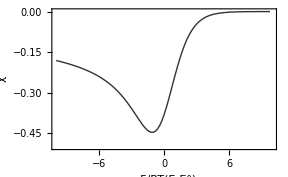

```mathematica
ListPlot[result,optionC]
```

Fig. 5.FigureCaption Linear sweep voltammogram simulated by solving the convolution integral using procedural implementation of Huber’s method.

### Chapter.Section.Subsection Functional Implementation of Huber’s Method

The procedural method is rather slow for evaluating larger data sets of say 400 to 800 points. Adopting a functional approach to solving the problem leads to some improvement in speed. In order to obtain a ‘feel’ for how eqn (Chapter.EquationNumbered) may be solved functionally we first expand it for the first few values of m.

a_1=g_1
a_2=g_2-a_1(2^(3/2)-1)
a_3=g_3-a_1(3^(3/2)-2^(3/2))-a_2(2^(3/2)-1)
a_4=g_4-a_1(4^(3/2)-3^(3/2))-a_2(3^(3/2)-2^(3/2))-a_3(2^(3/2)-1)
⋮
a_m=g_m-a_1(m^(3/2)-(m-1)^(3/2))-a_2((m-1)^(3/2)-(m-2)^(3/2))…-a_(m-1)(2^(3/2)-1)

Equation (Chapter.EquationNumbered) can be rearranged to give

a_1=g_1
a_1(2^(3/2)-1)+a_2=g_2
a_1(3^(3/2)-2^(3/2))+a_2(2^(3/2)-1)+a_3=g_3
a_1(4^(3/2)-3^(3/2))+a_2(3^(3/2)-2^(3/2))+a_3(2^(3/2)-1)+a_4=g_4
⋮
a_1(m^(3/2)-(m-1)^(3/2))+a_2((m-1)^(3/2)-(m-2)^(3/2))…+a_(m-1)(2^(3/2)-1)+a_m=g_m

The system of equations in (Chapter.EquationNumbered) can be expressed as the matrix equation Mat·a =g.

(1 | 0 | 0 | 0 |   | 0
(2^(3/2)-1) | 1 | 0 | 0 |   | 0
(3^(3/2)-2^(3/2)) | (2^(3/2)-1) | 1 | 0 |   | 0
(4^(3/2)-3^(3/2)) | (3^(3/2)-2^(3/2)) | (2^(3/2)-1) | 1 |   | 0
⋮ |   |   |   |   | ⋮
m^(3/2)-(m-1)^(3/2) | (m-1)^(3/2)-(m-2)^(3/2) |   | ⋯ | (2^(3/2)-1) | 1)(a_1
a_2
a_3
a_4
⋮
a_m)=(g_1
g_2
g_3
g_4
⋮
g_m)

with Mat being a lower diagonal matrix, i.e. a matrix with all the upper diagonal elements as zero and a and g are column vectors. Equation (Chapter.EquationNumbered) can be solved in Mathematica using the function LinearSolve that solves the matrix equation A·x=b for the unknown vector x. To begin with the vector g must first be generated

```mathematica
g:=Table[0.75/((1+Exp[10-i*d])*d^(3/2)),{i,n}];
```

The lower diagonal matrix Mat can be generated using the function LowerDiagonalMatrix. Let’s look at an example at how this function operates.

```mathematica
ClearAll[x,n,mat];

n=4;
mat=LowerDiagonalMatrix[x,n];
%//MatrixForm
```

(x[1,1] | 0 | 0 | 0
x[2,1] | x[2,2] | 0 | 0
x[3,1] | x[3,2] | x[3,3] | 0
x[4,1] | x[4,2] | x[4,3] | x[4,4])

The value of x[i,j] for each position in Mat can be assigned by generating a list containing the matrix elements from the bottom row of the matrix Mat, for example:

```mathematica
ClearAll[n,bottomRow];

n=4;
bottomRow=Table[((n-i+1)^(3/2)-(n-i)^(3/2))//N,{i,n,1,-1}]
```

{1.,1.82843,2.36773,2.80385}

The elements from the list bottomRow, that corresponds to the bottom row of matrix Mat, are ‘fed’ into the matrix.

```mathematica
x[r_,s_]:=bottomRow⟦r-s+1⟧;
n=4;
mat=LowerDiagonalMatrix[x,n];
%//MatrixForm
```

(1. | 0 | 0 | 0
1.82843 | 1. | 0 | 0
2.36773 | 1.82843 | 1. | 0
2.80385 | 2.36773 | 1.82843 | 1.)

Having generated Mat and g, eqn (Chapter.EquationNumbered) can be solved.

```mathematica
d=0.1;
a=LinearSolve[mat,g]
```

{0.00118994,-0.000860637,0.000209543,-0.000075567}

We have solved the vector a and are now able to solve for f(t).

```mathematica
Clear[f];

f=ConstantArray[0.,{n}];

f⟦1⟧=(d*a⟦1⟧);
```

In the final step we create a list of pairs of data for different values of m.

```mathematica
ClearAll[result];
result=Map[{10-(#*d),Sqrt[Pi]*Set[f⟦#⟧,(d*a⟦#⟧)+f⟦#-1⟧]}&,Range[2,n]]
```

{{9.8,0.0000583671},{9.7,0.0000955076},{9.6,0.0000821137}}

The full solution is outlined below.

```mathematica
ClearAll[d,n,g,bottom,x,mat,a,f,result];

d=0.2;
n=100;
g=Table[0.75/((1+Exp[10-i*d])*d^(3/2)),{i,n}];
bottom=Table[((n-i+1)^(3/2)-(n-i)^(3/2))//N,{i,n,1,-1}];
x[r_,s_]:=bottom⟦r-s+1⟧;
mat=LowerDiagonalMatrix[x,n];
a=LinearSolve[mat,g];

f=Table[0.,{n}];
f⟦1⟧=(d*a⟦1⟧);
result=Map[{10-(#*d),-Sqrt[Pi]*Set[f⟦#⟧,(d*a⟦#⟧)+f⟦#-1⟧]}&,Range[2,n]];
```

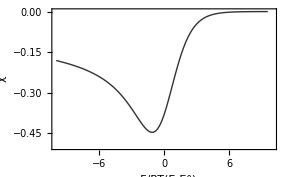

```mathematica
ListPlot[result,optionC]
```

Fig. 5.FigureCaption  Linear sweep voltammogram simulated by solving the convolution integral using functional implementation of Huber’s method.

## Chapter.Section Numerical solutions to Volterra equations of the second kind

Volterra equations of the second kind have the form

f(t)=g(t)+∫_0^t K(t,z)f(z)ⅆz

Following the same approach as in §5.2 the continuous function f(z) is replaced with the approximate function f_i for 1≤i≤m. This leads to the equation

f_0+d∑_(i=1)^m a_i=g(m d)+∑_(i=1)^m ∫_((i-1)d)^(i d) K(m d,z)(f_0+(z-i d)a_i+d∑_(j=1)^m a_j)ⅆz

from which, using the procedure outlined in §5.2 above, we obtain

f_0+d∑_(i=1)^m a_i=g(m d)+a_m h_1+f_0 r_m+∑_(i=1)^(m-1) a_i h_(m-i+1)

with

h_k=d[(kr)_k-(k-1)r_(k-1)]-s_k+s_(k+1)

For f_0=0 eqn (Chapter.EquationNumbered) can be rearranged to give

g(m d)=d∑_(i=1)^m a_i-(a_m h_1+∑_(i=1)^(m-1) a_i h_(m-i+1))

The equation to solve the second order Volterra equation differs from the solution to the first order Volterra equation only in the first term on the right hand side. Having written a program to solve the first order Volterra equation the solution to the second order Volterra equation therefore requires only minor changes.

## Chapter.Section Summary

In this chapter, the third of a block of three chapters providing an introduction to implementing numerical solutions to electrochemical problems in Mathematica, we examined methods to solve Volterra equations of the first and second kind and examined methods to set up the finite difference solution of quasi-reversible reactions. In the following chapters these tools are applied to simulating several types of one dimensional electrochemical experiments. Numerical methods are revisited when we consider coupled chemical reactions in Chapter 13.

## Further Reading

Britz, D. (1988). Digital Simulation in Electrochemistry, Springer-Verlag, Berlin.
Nicholson, R. S. and Shain, I. (1964). Analytical Chemistry, 36, 704-23.
Nicholson, R. S. (1965). Analytical Chemistry, 37, 1351-5.
Nicholson, R. S. and Olmstead, M. L. (1972). Numerical Solution of Integral Equations. In Electrochemistry; Calculations, Simulations, and Instrumentation, (eds. J. S. Mattson, H. B. Mark jnr., and H. C. MacDonald jnr.), pp. 119-38. Marcel Dekker, New York.
Press, W. H., Teukolsky, S. A., Vetterling, W. T., and Flannery, B. P. (1992). Numerical Recipes in C, (2nd edn). Cambridge University Press, New York.
Rudolph, M. (1995). Digital simulations with fast implicit finite difference algorithm: The development of a general simulator for electrochemical processes. In Physical Electrochemistry; Principles, Methods, and Applications, (ed. I. Rubenstein), pp. 81-130. Marcel Dekker, New York.
Rudolph, M. (1992). Journal of Electroanalytical Chemistry, 338, 85-98.